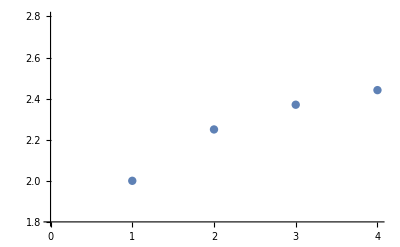

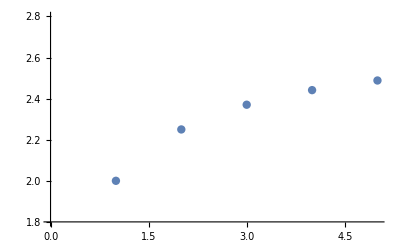

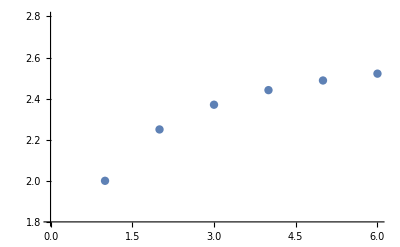

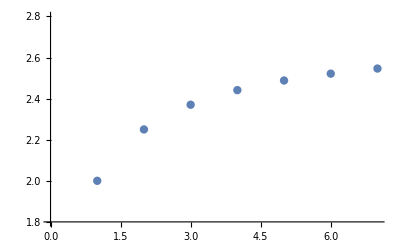

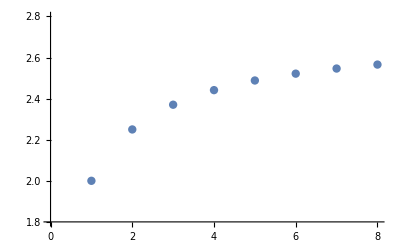

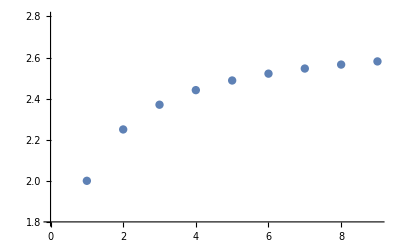

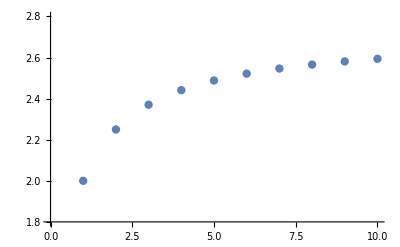

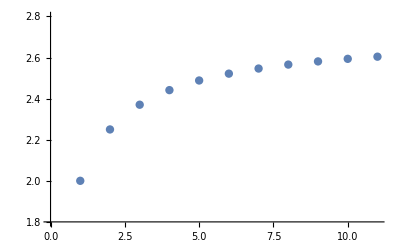

```mathematica
an ={(1+1/1)^1,(1+1/2)^2,(1+1/3)^3};
Do[an=Append[an,(1+1/i)^i];
t=ListPlot[an,PlotRange->{1.8,2.8},
PlotStyle->PointSize[0.015]];Print[t],{i,4,20}
]
```